```mathematica
data =Import["/Users/Nicolas/Documents/Research/Reason_Lab/icloud.nosync/actual-cause/experiment1/values.csv"]//Dataset
```

```mathematica
StimDataRaw = Floor[Normal[data]⟦3;;All,3;;7⟧]
```

{{1,0,1,1,2},{0,0,1,1,0},{0,1,1,0,2},{0,0,1,1,0},{0,0,1,0,0},{0,1,0,1,0},{0,1,1,0,2},{1,0,1,0,2},{0,0,1,0,0},{0,1,1,1,2},{0,0,1,1,0},{0,0,1,1,0},{1,0,1,0,2},{0,0,1,1,0},{0,0,0,1,0},{1,1,1,1,2},{0,0,1,1,0},{1,0,1,1,2},{1,0,1,0,2},{0,0,1,0,0}}

```mathematica
StimData = ((#*{1,2,3,4,5/2})+{0,0,0,0,5}&/@StimDataRaw)
```

{{1,0,3,4,10},{0,0,3,4,5},{0,2,3,0,10},{0,0,3,4,5},{0,0,3,0,5},{0,2,0,4,5},{0,2,3,0,10},{1,0,3,0,10},{0,0,3,0,5},{0,2,3,4,10},{0,0,3,4,5},{0,0,3,4,5},{1,0,3,0,10},{0,0,3,4,5},{0,0,0,4,5},{1,2,3,4,10},{0,0,3,4,5},{1,0,3,4,10},{1,0,3,0,10},{0,0,3,0,5}}

## Getting the indexes in sparse array representation

```mathematica
StimDataUnitary = (#*{1,1,1,1,1/2}&/@StimDataRaw)
```

{{1,0,1,1,1},{0,0,1,1,0},{0,1,1,0,1},{0,0,1,1,0},{0,0,1,0,0},{0,1,0,1,0},{0,1,1,0,1},{1,0,1,0,1},{0,0,1,0,0},{0,1,1,1,1},{0,0,1,1,0},{0,0,1,1,0},{1,0,1,0,1},{0,0,1,1,0},{0,0,0,1,0},{1,1,1,1,1},{0,0,1,1,0},{1,0,1,1,1},{1,0,1,0,1},{0,0,1,0,0}}

```mathematica
targets=Keys[Normal[ArrayRules[SparseArray[StimDataUnitary]]]][[;;-2]]-1
```

{{0,0},{0,2},{0,3},{0,4},{1,2},{1,3},{2,1},{2,2},{2,4},{3,2},{3,3},{4,2},{5,1},{5,3},{6,1},{6,2},{6,4},{7,0},{7,2},{7,4},{8,2},{9,1},{9,2},{9,3},{9,4},{10,2},{10,3},{11,2},{11,3},{12,0},{12,2},{12,4},{13,2},{13,3},{14,3},{15,0},{15,1},{15,2},{15,3},{15,4},{16,2},{16,3},{17,0},{17,2},{17,3},{17,4},{18,0},{18,2},{18,4},{19,2}}

```mathematica
SetDirectory["~/Documents/Research/Reason_Lab/icloud.nosync/actual-cause/experiment1"]
Directory[]
```

/Users/Nicolas/Documents/Research/Reason_Lab/icloud.nosync/actual-cause/experiment1

/Users/Nicolas/Documents/Research/Reason_Lab/icloud.nosync/actual-cause/experiment1

#### Save target indexes to csv

```mathematica
Export[Directory[]<>"/values.json",targets,"JSON"]
```

/Users/Nicolas/Documents/Research/Reason_Lab/icloud.nosync/actual-cause/experiment1/values.json

```mathematica
RGB8Bit[r_,g_,b_]:=RGBColor@@({r,g,b}/255)
```

```mathematica
colormap = {3->RGB8Bit[255,255,130],2->RGB8Bit[139,148,163],4->RGB8Bit[177,142,242],1->RGB8Bit[230,95,92],5->Green,10->Darker[Blue]}
```

{3→RGBColor[1, 1, Rational[26, 51]],2→RGBColor[Rational[139, 255], Rational[148, 255], Rational[163, 255]],4→RGBColor[Rational[59, 85], Rational[142, 255], Rational[242, 255]],1→RGBColor[Rational[46, 51], Rational[19, 51], Rational[92, 255]],5→RGBColor[0, 1, 0],10→RGBColor[0, 0, Rational[2, 3]]}

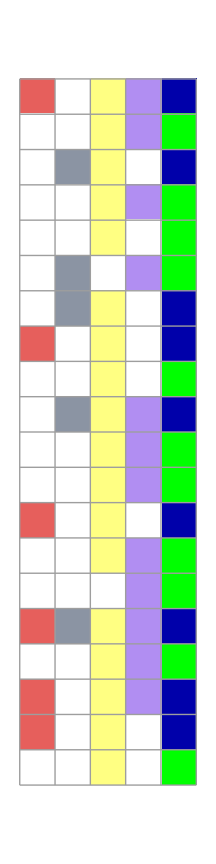

```mathematica
ArrayPlot[StimData,ColorRules->colormap,Mesh->True]
```

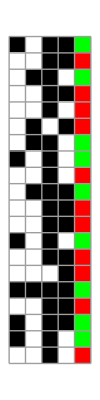

```mathematica
ArrayPlot[StimData,ColorRules->{10->Green,5->Red,1->Black,2->Black,3->Black,4->Black},Mesh->True]
```

## Just messing around

```mathematica
#1->#2&[1,4]
```

1→4

```mathematica
[1,2]
```

1→2

```mathematica
Inner[#1->#2&,{a,b,c},{d,e,f},List]
```

{a→d,b→e,c→f}

```mathematica
Inner[#1->#2&,Table[1,16],Values[sims],List]
```

{1→1480,1→2168,1→2158,1→540,1→1435,1→355,1→164,1→494,1→334,1→64,1→230,1→46,1→193,1→239,1→61,1→39}

```mathematica
8
```

<|{1,0,1,0}→1480,{0,0,1,1}→2168,{0,0,1,0}→2158,{0,1,1,0}→540,{1,0,1,1}→1435,{1,1,1,1}→355,{1,0,0,1}→164,{0,1,1,1}→494,{1,1,1,0}→334,{0,1,0,1}→64,{0,0,0,0}→230,{1,1,0,1}→46,{1,0,0,0}→193,{0,0,0,1}→239,{0,1,0,0}→61,{1,1,0,0}→39|>

<|{1, 1, 0, 0}→39,{1, 1, 0, 1}→46,{0, 1, 0, 0}→61,{0, 1, 0, 1}→64,{1, 0, 0, 1}→164,{1, 0, 0, 0}→193,{0, 0, 0, 0}→230,{0, 0, 0, 1}→239,{1, 1, 1, 0}→334,{1, 1, 1, 1}→355,{0, 1, 1, 1}→494,{0, 1, 1, 0}→540,{1, 0, 1, 1}→1435,{1, 0, 1, 0}→1480,{0, 0, 1, 0}→2158,{0, 0, 1, 1}→2168|>

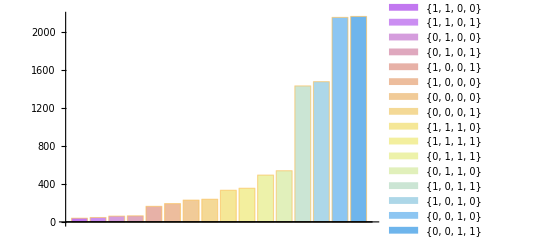

```mathematica
sims =Counts[Table[Table[RandomVariate[BernoulliDistribution[x]],{x,{0.4,0.2,0.9,0.5}}],10000]]


KeyMap[ToString,sims]//Sort
BarChart[%,ChartLegends->Keys[%],ChartStyle->"Pastel"]
```

```mathematica
Map[,Keys[sims]]
```

{f[{1,0,1,0}],f[{0,0,1,1}],f[{0,0,1,0}],f[{0,1,1,0}],f[{1,0,1,1}],f[{1,1,1,1}],f[{1,0,0,1}],f[{0,1,1,1}],f[{1,1,1,0}],f[{0,1,0,1}],f[{0,0,0,0}],f[{1,1,0,1}],f[{1,0,0,0}],f[{0,0,0,1}],f[{0,1,0,0}],f[{1,1,0,0}]}

```mathematica
1∨0//Evaluate
```

1||0

```mathematica
Join[{1},{2}]
```

{1,2}

{{1,0,1,0,1},{0,0,1,1,0},{0,0,1,0,0},{0,1,1,0,1},{1,0,1,1,1},{1,1,1,1,1},{1,0,0,1,0},{0,1,1,1,1},{1,1,1,0,1},{0,1,0,1,0},{0,0,0,0,0},{1,1,0,1,0},{1,0,0,0,0},{0,0,0,1,0},{0,1,0,0,0},{1,1,0,0,0}}

```mathematica
Join[#,[Keys[sims]]&/@
```

{{1,0,1,0},{0,0,1,1},{0,0,1,0},{0,1,1,0},{1,0,1,1},{1,1,1,1},{1,0,0,1},{0,1,1,1},{1,1,1,0},{0,1,0,1},{0,0,0,0},{1,1,0,1},{1,0,0,0},{0,0,0,1},{0,1,0,0},{1,1,0,0}}

{1,0,0,1,1,1,0,1,1,0,0,0,0,0,0,0}